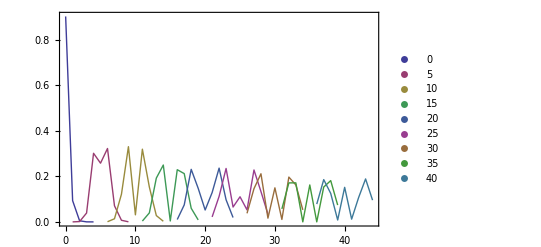

0.951734

```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"]
nCutoff=40;
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;λ=852nm;
(*raman w/l*)ω=2π 20kHz;
(*trap freq*)θ=.67 ArcTan[10/11]; (*angle in rad b/t 2 axial raman beams*) (*recalibrated based on 9/28 msmt to give 150 us sb pi time at 3.7 nbar and 50us carrier pi time*)
z0=√(ℏ/(2 mCs ω));ηR=Δk z0;ηOP=k0 z0;k0=(2π)/λ;
Δk=k0 Sin[θ];

μ[m_,n_,η_]:=Exp[-η^2/2] √((nMin!)/(nMax!))η^(nMax-nMin)LaguerreL[nMin,nMax-nMin,η^2]/.nMin->Min[m,n]/.nMax->Max[m,n];

SBs[n_]:=Cases[Table[{n+order,μ[n,n+order,ηOP]^2},{order,-4,4}],x_/;Head[x[[2]]]==Real]; (*only keep real results (ie ignore n<0 etc)*)

Ns=Range[0,40,5];
ListPlot[SBs[#]&/@Ns,Joined->True,PlotLegends->Ns,PlotRange->All]
Total[SBs[40][[;;,2]]] (*close to 100%?*)
```

```mathematica
SBs[0]
```

{{0,0.901765},{1,0.0932434},{2,0.00482073},{3,0.000166156},{4,4.29518×10^-6}}

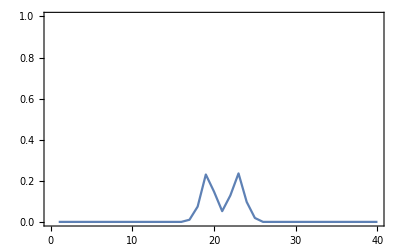

```mathematica
(*test on initial fock state*)
n=20;
occ=Normal[SparseArray[n+1->1,40]];
Clear[n]
occ2=0occ; (*clear temporary register*)
Do[(*loop over all n*)
Do[(*loop over all i in SB[n]*)
If[i+1≤Length[occ],
(*i,n+1 is because i=1 is for n=0*)
occ2[[i+1]]+=occ[[n+1]]Cases[SBs[n],x_/;x[[1]]==i][[1,2]]
]
,{i,SBs[n][[;;,1]]}];
,{n,0,Length[occ]-1}];
occ=occ2;
ListPlot[occ,PlotRange->{All,{0,1}},Joined->True]
```